## Usage of Mathematica

From the Help Menu open the Documentation Center. Under Resources you can find two Fast Introductions, for Programmers and for Math students. Both are worthwhile. To learn the  syntax selected exercises will be given.

## Linear Differential Equations

As an exercise two difficult linear differential equations will be solved analytically, and examples of the solutions will be plotted.

For any new function that you use, first read the manual page. You can easily read the manual page by clicking the word DSolve in your notebook and press F1. 
Mathematica is case sensitive. Note that all functions start with a capital, and arguments of functions are in square brackets [ ]. 
Single = represents an assignment, and creates a global variable with that value.
Double == represents an equation. If you make a mistake, and forget an =, you will get an error message from DSolve. Then you can remove all global variables using:

```mathematica
Remove["Global`*"]
```

Always give names (with 2 or more characters) to your output objects to facilitate their usage. 
Use // Flatten after DSolve  to remove the double curly brackets { } that indicate a double list.

## Impulse response of a first order system

-Graphics-

Retype the above input line yourself in the input cell below and check that it works.

```mathematica
ht = DSolveValue[{y'[t]+y[t]/τ==DiracDelta[t], y[0]==HeavisideTheta[0]},y[t], t]//Flatten
```

ⅇ^(-t/τ) HeavisideTheta[t]

To insert a Greek letter use the Palette  Basic Math Assistant, the 2nd tab under typesetting, and click the symbol τ . If you hover with your mouse over the symbol τ, you see the shortcut Esc - t - Esc .

Make a list (using { and } or List) called values with a substitution rule for  τ equal to 1

Retype the above input line yourself (the arrow is a hyphen followed by >) in the input cell below and check that it works.

```mathematica
values = {τ->1}
```

{τ→1}

Now apply values to ht, name the output object ht1.

```mathematica
ht1 = ht /.values
```

ⅇ^-t HeavisideTheta[t]

Plot the impulse response ht1 for 3 s, with PlotOption AxesLabel→Automatic.

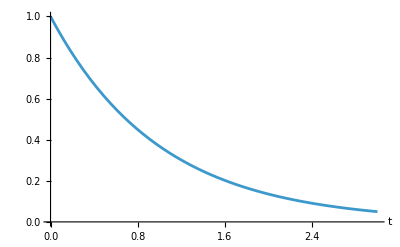

```mathematica
Plot[ht1, {t,0,3}, AxesLabel ->Automatic]
```

Use Manipulate to draw the impulse response for different values of τ and end time tend.

```mathematica
Manipulate[Plot[ht/.{τ->a},{t,0,tend},AxesLabel->Automatic, PlotRange->{0,1}],{{a,1},0.1,10},{{tend,3},0.1,100}]
```

```mathematica
DynamicModule[{a=1,tend=3},Plot[ht/.{τ->a},{t,0,tend},AxesLabel->Automatic,PlotRange->{0,1}]]
```

Check the manual page of Manipulate and make sure that you completely understand the above input line, and the working of the controls a and tend.

Retype the above input line yourself in the input cell below and check that it works.

Finally, we write a function modfirst using Module with as arguments τ and tend to compute the impulse response and plot it. Complete the definition of modfirst and check that it works and that you  can reproduce the plot of ht1.

```mathematica
modfirst[τ_,tend_]:=Module[{ht}, DSolveValue[{y'[t]+y[t]/τ==DiracDelta[t], y[0]==HeavisideTheta[0]},y[t], t];
Plot[ht,{t,0,tend},AxesLabel->Automatic,PlotRange->{0,1}]]
```

Note that the semicolon ; which is the CompoundExpression symbol is crucial to ensure that the second argument of Module is a single expression.

Use Manipulate with modfirst to draw the impulse response for different values of τ and end time tend.

```mathematica
Manipulate[modfirst[a,tend],{{a,1},0.1,10},{{tend, 3},0.1,100}]
```

Note that when you use the same name for the rule object, it also affects the previous Manipulate plot. In order to avoid this one can either use a local variable name for the rule, or name the object differently.

## Step response of a first order system

There are two ways to compute the step response, first by integration of the impulse response, since the step is the integral of the unit impulse. Integrate ht and name the output object s1t.

```mathematica
s1t =Integrate[ht, t]
```

(τ-ⅇ^(-t/τ) τ) HeavisideTheta[t]

Now apply values to s1t, name the output object s1t1 and plot object s1t1.

```mathematica
s1t1 = s1t/.values
```

(1-ⅇ^-t) HeavisideTheta[t]

Second, by solving the differential equation with as input the HeavisideTheta function and with initial condition zero. Name the output object s2t.

```mathematica
s2t = DSolveValue[{y'[t]+y[t]/τ == HeavsideTheta[t], y[0]==0}, y[t], t]//Simplify
```

ⅇ^(-t/τ) ⅇ^(K[1]/τ) HeavsideTheta[K[1]]K[1]0t

Now apply values to s2t, name the output object s2t1 and plot the object s2t1 .

```mathematica
s2t1 = s2t /.values
```

ⅇ^-t ⅇ^K[1] HeavsideTheta[K[1]]K[1]0t

Now plot the difference s1t1 minus s2t1 .

```mathematica
Plot[s2t1-s1t1,{t,0,3}, PlotRange ->All]
```

-Graphics-

The difference is numerical imprecision (16 th decimal place) .

## Nonlinear Differential Equations

When you try to solve a nonlinear differential equation using DSolve most often you will not find a solution. When no analytical solution (which is applicable for all parameter values and all times) can be found, we must solve numerically (which means that we must choose the time interval and parameter values beforehand).

## The SIR model

The simplest SIR model consists of three compartments: susceptible, s(t); infected, i(t); and recovered, r(t) (note the lowercase r). The three compartments are described by three coupled nonlinear ordinary differential equations (ODEs): s'(t) = -R0*γ*i(t)*s(t), i'(t) = R0*γ*i(t)*s(t) - γ*i(t) and r'(t) = γ*i(t). The model contains only two parameters: the reproduction number R0 (note the uppercase R in R0) and the recovery rate γ. The initial conditions are s(0) = s0, r(0) = r0 en i(0) = i0 . Because of the nonlinearity we will solve the coupled nonlinear ordinary differential equations numerically use NDSolve. Because we have to solve numerically all the values of parameters, initial conditions and the time interval have to be known beforehand.

Make a list (using {and} or List) called values with substitution rules for s0=1, r0=0, i0 = 10^-5, tend = 40, γ = 1/7, R0 = 10

-Graphics-

Retype the above input line yourself in the input cell below and check that it works.

```mathematica
values = {s0->1, i0->10^-5,r0->0, tend->40, γ->1/7, R0->10}
```

{s0→1,i0→1/100000,r0→0,tend→40,γ→1/7,R0→10}

Now solve the coupled nonlinear ordinary differential equations numerically using NDSolveValue for time from 0 until the end time tend

-Graphics-

Retype the above input line yourself in the input cell below and check that it works.

```mathematica
{st,it,rt}=NDSolveValue[
{s'[t]==-R0*γ*s[t]*i[t],
i'[t]==R0*γ*s[t]*i[t]-γ*i[t],
r'[t]==γ*i[t],
s[0]==s0,
i[0]==i0,
r[0]==r0}/.values,
{s[t],i[t],r[t]},
{t,0,tend/.values}]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

Now plot this list from 0 until the end time tend, with PlotOption PlotLegends→”Expressions”

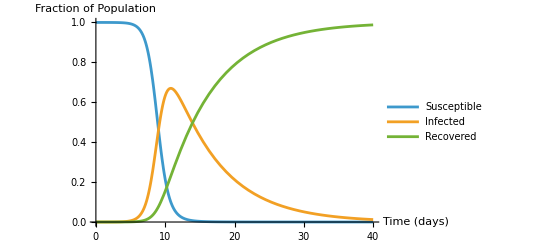

```mathematica
Plot[{st,it,rt},{t,0,tend/.values},PlotLegends->{"Susceptible", "Infected","Recovered"},AxesLabel ->
{"Time (days)","Fraction of Population"}]
```

Your plot should look like this

-Graphics-

To compute the final values {stend,itend,rtend}, you can use a substitution rule that replaces t by tend in the objects {st,it,rt}, and apply values:

-Graphics-

```mathematica
{stend, itend, rtend}={st,it,rt}/.{t->tend/.values}
```

{0.0000513188,0.0122203,0.987738}

To find the maximum value of it use the function FindMaximum, starting from a properly selected time point:

```mathematica
max= FindMaxiumum[it[t],{t,10}]
```

FindMaxiumum[InterpolatingFunction[…][t][t],{t,10}]

```mathematica
Remove["Global`*"]
```

Write a function called modSIR that uses Module, with as arguments i0, γ, R0, tend, s0 and r0, with default values 1/90, 1/4, 4/3 (note that it is not permitted to use here the expression (1/(3γ )), (7*14),1 and 0.
Check that you can reproduce the previous plot.

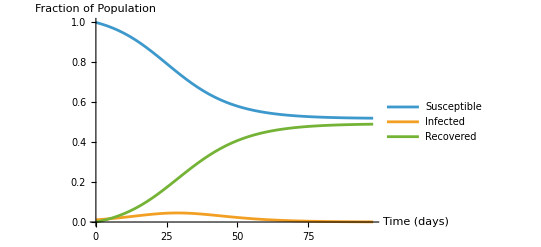

```mathematica
modSIR[i0_:1/90,γ_:1/4,R0_:4/3,tend_:(7*14),s0_:1,r0_:0]:=Module[{},{st,it,rt}=NDSolveValue[
{s'[t]==-R0*γ*s[t]*i[t],
i'[t]==R0*γ*s[t]*i[t]-γ*i[t],
r'[t]==γ*i[t],
s[0]==s0,
i[0]==i0,
r[0]==r0},
{s[t],i[t],r[t]},
{t,0,tend}];
Plot[{st,it,rt},{t,0,tend},PlotLegends->{"Susceptible", "Infected","Recovered"},AxesLabel ->
{"Time (days)","Fraction of Population"}]]
modSIR[]
```

Now use Manipulate to study modSIR with controls for R0 and tend (to make sure you reach the final state). Keep i0 = 10^-4, γ = 1/7, which are different from the previously used values. Use Paste Snapshot (click on the top right plus symbol) to produce plots for two interesting values of R0, 1.1 and 0.999

```mathematica
Manipulate[modSIR[10^-4,1/7,R0,tend],{R0,0,10},{tend,1,1000}]
```

Write a function called modSIRend which is a modification of modSIR that returns only the value rtend, i.e. the fraction of the population that has been infected and either recovered or deceased. Test that it produces the right output with the default values.

```mathematica
modSIRend[i0_:1/90,γ_:1/4,R0_:4/3,tend_:(7*14),s0_:1,r0_:0]:=
Module[{},{st,it,rt}=NDSolveValue[
{s'[t]==-R0*γ*s[t]*i[t],
i'[t]==R0*γ*s[t]*i[t]-γ*i[t],
r'[t]==γ*i[t],
s[0]==s0,
i[0]==i0,
r[0]==r0},
{s[t],i[t],r[t]},
{t,0,tend}];rtend = rt/.{t->tend}]
```

Now make a plot of modSIRend with R0 from 0 to 5, with i0 = 10^-4, γ = 1/7,  tend = 10000/R0.

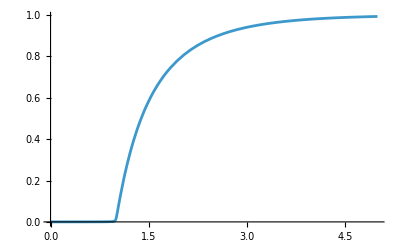

```mathematica
Plot[modSIRend[10^-4,1/7,R0,10000/R0],{R0,0,5}]
```

Now make another plot of modSIRend with R0 from 0 to 0.999, with i0 = 10^-4, γ = 1/7,  tend = 10000/R0.

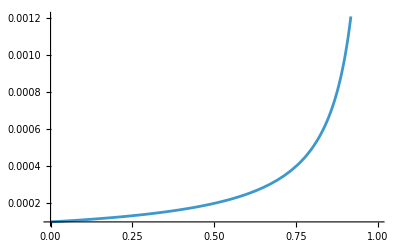

```mathematica
Plot[modSIRend[10^-4,1/7,R0,10000/R0],{R0,0,0.999}]
```

Now make a LogPlot of modSIRend with R0 from 0 to 5, with i0 = 10^-4, γ = 1/7,  tend = 10000/R0.

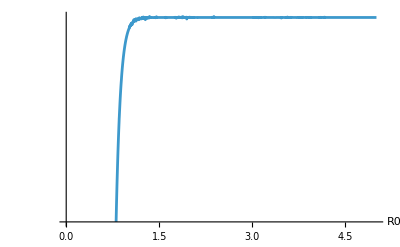

```mathematica
LogPlot[modSIRend[10^-4, 1/7. R0, 10000/R0],{R0,0,5},AxesLabel->Automatic, PlotLegends ->"r(tend)"]
```